# Corner Convergence

The convergence is easily computable if the min is in a corner.  The algorithm gives better than the diagonal path that we can easily explicitly compute and illustrate.  It seems as though a corner min is the worst for the interior point scheme and best for gradient projection.

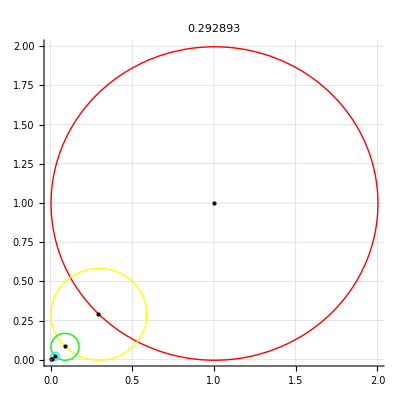

```mathematica
Clear[r2,c2]
r2[k_]:= (1-1/(√2))^k
c2[k_]:=r[k]{1,1} 
Graphics[Table[
{Point[c2[k]],{Hue[k/6],Circle[c2[k],r2[k]]}},
{k,0,5}],
Axes->True,GridLines->Automatic,PlotLabel->N[r2[1]]]
```

```mathematica
r3[k_]:= (1-1/(√3))^k
c3[k_]:=r3[k]{1,1,1} 
Graphics3D[Table[
{Point[c3[k]],{Opacity[0.5],Hue[k/6],Sphere[c3[k],r3[k]]}},
{k,0,5}],
Axes->True,PlotLabel->N[r3[1]]]
```

-Graphics3D-

Deflation factor for an n dimensional corner approached along the diagonal is 
	(1-1/(√n))

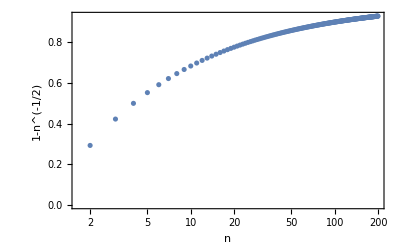

```mathematica
ListLogLinearPlot[
Table[{n,N[1-1/(√n)]},{n,2,200}],
PlotRange->All,Frame->True,
GridLines->Automatic,
FrameLabel->{"n","1-n^(-1/2)"}
]
```

This is not good for a highish dimensional corner approached along the diagonal.

# Projected Gradient

Reminder:  In this context the Cauchy Point from a point x_k is the first local min of f(x_k+d(t) ) where d(t) is simply the steepest decent direction 
	d_k=-∇f(x_k) 
projected face by face onto the constraint box l≤x≤u. The Cauchy Point is an easily computed point sufficiently improved from x_k to ensure convergence.  Once you have found the Cauchy point you run a minimization algorithm (no need to do it to convergence) with the active set identified by the Cauchy point.  Then you either work out which of the currently active constraints to turn off (compute the multipliers and deactivate the ones with the wrong sign) or just turn them all off by moving the approximate local min z_(k+1) satisfying the active constraints a little bit into the interior of the box.  The easiest way to do this would be to move z_(k+1) a distance ϵ towards the center c=0.5(l+u) of the box
	x_(k+1)=z_(k+1)+ϵ (c-z_(k+1)).
This is automatically an interior point.  The idea is that it is fast to run the Cauchy point computation again which will turn the appropriate constraints back on.

A plausible “hybrid” algorithm would run the “Cauchy Point” projection, “interiorize” the border point by an amount within our constraint tolerance, and then run the Elliptical Constraint construction and minimization.  The constraint computation always satisfies the elliptical constraint to full precision and the elliptical constraint is within the constraint box.

```mathematica
Clear[c]
{l,u}={{1,2},{5,19}};
c=0.5 (l+u)
xk={1,5};
ϵ=0.1;
xk+ϵ (c-xk)
```

{3.,10.5}

{1.2,5.55}